# HW 4

Generate a random 6×12 matrix called A and compute the SVD.  Use standard names for the factors.

Demonstrate that the U and V matrices satisfy the appropriate orthogonality conditions.

Plot the inner matrix and print the singular values.

Demonstrate that A equals the appropriate product of the SVD factors.

How should I choose x with ||x(||)_2=1 to make ||A.x(||)_2 as big as possible.

How should I choose x with ||x(||)_2=1 to make ||A.x(||)_2 as small as possible

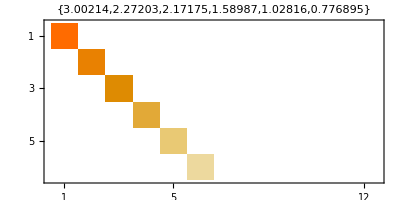

2.44142×10^-15

```mathematica
{m,n}={6,12}; A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
MatrixPlot[S,PlotLabel->Diagonal[S]]
Norm[A-U.S.Vᵀ]
```

```mathematica
?Eigensystem
```

The largest and smallest singular values are the largest and smallest output sizes. They come from the first and last vs respectively

```mathematica
vBig=V⟦All,1⟧;
Map[Norm,{vBig,A.vBig}]
```

{1.,3.5061}

```mathematica
vZero=V⟦All,-1⟧;
Map[Norm,{vZero,A.vZero}]
```

{1.,5.33889×10^-16}

```mathematica
vSmall=V⟦All,6⟧;
Map[Norm,{vSmall,A.vSmall}]
```

{1.,0.61747}

Generate a random 6×6 matrix called A and compute the SVD and eigenvalue decompositions of A. Use standard names for the factors.

Demonstrate that A equals the appropriate product of the SVD factors.

Demonstrate that A equals the appropriate product of the eigen decomposition factors.

Are the eigenvalues real?

Is the matrix of eigenvector orthogonal?

How should I choose x with ||x(||)_2=1 to make ||A.x(||)_2 as big as possible.

How should I choose x with ||x(||)_2=1 to make ||A.x(||)_2 as small as possible

The decompositions match

```mathematica
{m,n}={6,6}; A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
{lambdas,X}=Eigensystem[A]; X=Xᵀ;
Map[Norm,{A-U.S.Vᵀ, A-X.DiagonalMatrix[lambdas].Inverse[X]}]
```

{2.28485×10^-15,3.15085×10^-15}

The eigenvalues are not real!

```mathematica
lambdas
```

{0.21878+1.1846 ⅈ,0.21878-1.1846 ⅈ,-1.16038,1.13623,-0.468402+0.568973 ⅈ,-0.468402-0.568973 ⅈ}

The eigenvectors are NOT orthogonal!

```mathematica
Norm[X.Xᵀ-IdentityMatrix[m]]
OrthogonalMatrixQ[X]
```

1.8129

False

There is no null space and the singular values now give the extreme values!

```mathematica
vBig=V⟦All,1⟧;
Map[Norm,{vBig,A.vBig}]
```

{1.,2.53436}

```mathematica
vSmall=V⟦All,m⟧;
Map[Norm,{vSmall,A.vSmall}]
```

{1.,0.380393}